```mathematica
nmax= 10
Manipulate[Plot[{1,x^n/Factorial[n]},{x,0,nmax}],{n,0,nmax}]
```

10

```mathematica
Plot3D[{1,x^n/Factorial[n]},{x,0,nmax},{n,0,nmax}]
```

-Graphics3D-

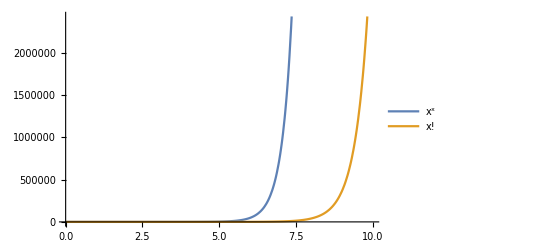

```mathematica
Plot[{x^x,Factorial[x]},{x,0,nmax},PlotLegends->"Expressions"]
```

300

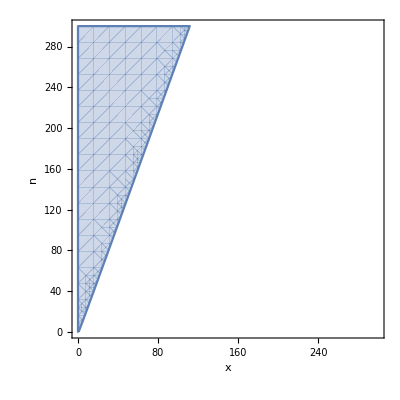

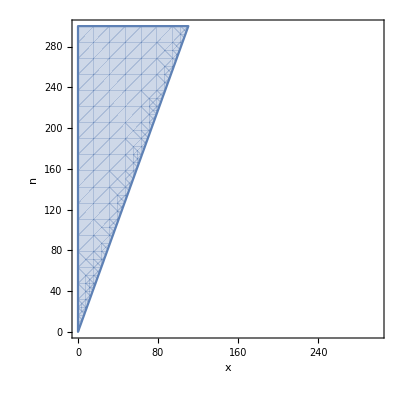

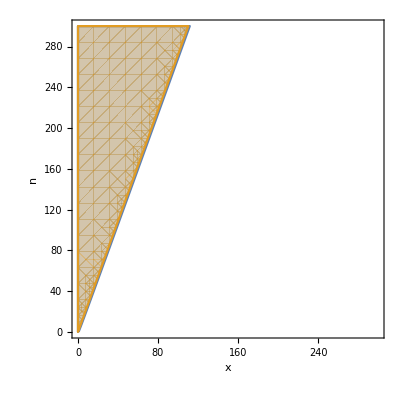

```mathematica
nmax=300
RegionPlot[x^n<Factorial[n],{x,0,nmax},{n,0,nmax},AxesLabel->{"x","n"}]
RegionPlot[x*Exp[1]<n,{x,0,nmax},{n,0,nmax},AxesLabel->{"x","n"}]
RegionPlot[{x^n<Factorial[n],x*Exp[1]<n},{x,0,nmax},{n,0,nmax},AxesLabel->{"x","n"}]
```

```mathematica
Limit[x^n/Factorial[n],n->∞]
```

0

```mathematica
Manipulate[Plot[x^n/Factorial[n],{n,0,x*Exp[1]*2},GridLines->{{Exp[1]*x},{1}}],{x,0.1,10}]
```